# Benthic v. Pelagic Encounter Rates

```mathematica
ClearAll["Global`*"]
```

#### Parameter Declaration

```mathematica
(* Population Constants *)
mN= 0.05; (* 0-0.25 per cm^2, Total mysid density - O'Malley et al. (2018) *)
sculN =0.00000001; (* Sculpin population density (#/cm^2) - Bowers et al. (1990) *)
smeltN =0.00000015; (* Smelt population density (#/cm^3) - Stritzel Thomson et al. (2011) *)

(* Migration Constants *)
tempdepth = 20; 
(* Boscarino et al. (2010), O'Malley & Stockwell (2019) *)
lightdepth = 40; (* Gal et al. (2004) *)
dsens = 10^7; (* Turbidity *)

(* Size Constants *)
sculL = 8.0; (* Janssen (1990), Janssen & Corcoran (1998) *)
sculD = 29.0; (* Sculpin detection radius in cm - Janssen (1990) *)
sculmin = 2.0; (* minimum sculpin detection radius in cm *)
smeltL = 9.0;  (* Coughlin et al. (1999)*)
smeltD = smeltL^1.1;  (* Smelt detection radius in cm - Ware (1978) *)

(* Motion Constants *)
smv = 1.5;  (* ~0.5-5,
 Small mysid velocity in cm/sec - Bowers et al.(1990) *)
bmv = 2.5; (* ~0.5-5, Big mysid velocity in cm/sec - Bowers et al.(1990) *)
sculv = 4* sculL; 
scultmax = 2.0; 
smeltv = 15;
```

```mathematica
(* Predation constants *)
sculH = 0.56; (* Sculpin handling time, SECONDS, DOI: 10.14288/1.0095873 *)
sculESlarge = 0.1385; (* Sculpin encounter success *)
sculESsmall = 0.277; (* Sculpin encounter success *)

smeltH = 0.76; (* alewife handling time, SECONDS,  DOI: https://doi.org/10.1007/BF00005177 *)
smeltESlarge = 0.72; 
smeltESsmall = 0.36;
```

## Functions

### Benthic ER

```mathematica
(* Circles & Velo *)
Velo[s_,tmax_, maxv_]:=(maxv s^2)/(tmax + s^2);
Aint[tmax_, maxv_,s_, Dd_]:= -1/2 Velo[s,tmax, maxv]*s √(4 Dd^2-(Velo[s,tmax, maxv]*s )^2)+2 Dd^2 ArcCos[(Velo[s,tmax, maxv]*s)/(2 Dd)];

(* Continuous - Stationary *)
C2D[dens_,s_,tmax_,maxv_, Dd_]:= 2 dens Dd Velo[s,tmax,maxv];

(* Discrete - Stationary *)
D2D[dens_,s_, Dd_]:= (dens π Dd^2)/s;
(* Intermediate - Stationary *)
I2D[dens_,s_,tmax_, maxv_, Dd_]:=(dens (π Dd^2 - Re[Aint[tmax,maxv,s,Dd]]))/s;
(* Continuous - Mobile (same as M2D, but with sculpin params *)
C2Dm[dens_,u_,s_,tmax_,maxv_, Dd_]:=1/π 2 dens Dd(√((u-Velo[s,tmax,maxv])^2) EllipticE[-(4 u Velo[s,tmax,maxv])/(u-Velo[s,tmax,maxv])^2]+√((u+Velo[s,tmax,maxv])^2) EllipticE[(4 u Velo[s,tmax,maxv])/(u+Velo[s,tmax,maxv])^2]);
(* C2Dm when v = 0: - *)
FullSimplify[1/π 2 dens Dd(√((u-v)^2) EllipticE[-(4 u v)/(u-v)^2]+√((u+v)^2) EllipticE[(4 u v)/(u+v)^2]),v==0]
(* Discrete - Mobile *)
D2Dm[dens_,u_,s_,tmax_, maxv_, Dd_]:= 1/s 1/π 2 dens Dd(√((u-Velo[s,tmax,maxv])^2) EllipticE[-(4 u Velo[s,tmax,maxv])/(u-Velo[s,tmax,maxv])^2]+√((u+Velo[s,tmax,maxv])^2) EllipticE[(4 u Velo[s,tmax,maxv])/(u+Velo[s,tmax,maxv])^2]);
(* Intermediate - Mobile *)
I2Dm[dens_,u_,s_,tmax_, maxv_, Dd_]:=2 Dd dens u( Re[Aint[tmax,maxv,s,Dd]]/(π Dd^2))+D2Dm[dens,u,s,tmax, maxv, Dd](1-Re[Aint[tmax,maxv,s,Dd]]/(π Dd^2));
```

2 Dd dens √(u^2)

### Pelagic ER

#### Stationary

```mathematica
S2D[dens_,v_, rad_]:= 2 dens rad v;
S3D[dens_,v_, rad_]:=  π rad^2 dens v;
```

#### Mobile

```mathematica
M2D[dens_, v_,u_,rad_]:=1/π 2 dens rad (√((u-v)^2) EllipticE[-(4 u v)/(u-v)^2]+√((u+v)^2) EllipticE[(4 u v)/(u+v)^2]);
M3D[dens_,v_,u_,rad_]:=  Piecewise[{{(π rad^2 dens)/3((u^2+3 v^2)/v), u<v},{(π rad^2 dens)/3((v^2+3 u^2)/u), u >= v}}];
```

### Functional responses

```mathematica
T2[er_,es_,h_] := (er es)/(1 + er es h);(* Encounter rate accounts for density *)
```

### Migration

```mathematica
maxD[t_,dep_, dsens_]:= smeltD - (smeltD dep^4)/(dsens+ dep^4);
SmeltD[t_,dep_,dsens_]:=1/2((maxD[t,dep,dsens]-1.5) Sin[0.261796(t-1) + 3Pi/2]+(1.5+maxD[t,dep,dsens]));
```

```mathematica
mornstart1 = 6.5;
mornend1 = 7.5;
evestart1 = 18.5;
eveend1 = 19.5;
mornstart2 = 30.5;
mornend2 = 31.5;
evestart2 = 42.5;
eveend2 = 43.5;
```

```mathematica
depx[t_] := Piecewise[{
{tempdepth, 0<t<=mornstart1},
{(85-tempdepth)(t-mornend1 ) + 85, mornstart1 <t<=mornend1 },
{85, mornend1<t<=evestart1},
{-(85-tempdepth)(t-eveend1)+tempdepth, evestart1<t<=eveend1 },
{tempdepth, eveend1<t<=mornstart2},
{(85-tempdepth)(t-mornend2)+ 85, mornstart2<t<=mornend2},
{85, mornend2<t<=evestart2},
{-(85-tempdepth)(t-eveend2)+tempdepth, evestart2<t<=eveend2},
{tempdepth, eveend2<t<=48}
}];
```

```mathematica
pelint[t_?NumericQ,mp_?NumericQ,sN_?NumericQ,mN_?NumericQ, v_?NumericQ]:= sN*T2[M3D[mp * mN/4,v,bmv,SmeltD[t,depx[t],dsens]],smeltES,smeltH];

benint[t_?NumericQ,migprop_?NumericQ,mN_?NumericQ,sculN_?NumericQ,s_?NumericQ]:=sculN*T2[(Re[I2Dm[(1-migprop)*mN/2,0,s,scultmax,sculv,sculD]]+C2Dm[(1-migprop)*mN/2,bmv,s,scultmax,sculv,sculmin]),sculES,sculH];

benalt[t_?NumericQ,migprop_?NumericQ,mN_?NumericQ,sculN_?NumericQ,s_?NumericQ]:=sculN*T2[(C2Dm[(1-migprop)*mN/2,0,s,scultmax,sculv,sculD]+C2Dm[(1-migprop)*mN/2,bmv,s,scultmax,sculv,sculmin]),sculES,sculH];
```

### Utility

```mathematica
restylePlot[p_,op:OptionsPattern[ListLinePlot]]:=ListLinePlot[Cases[Normal@p,Line[x__]:>x,∞],op,Options[p]]
```

## Encounter Rates

#### M2D

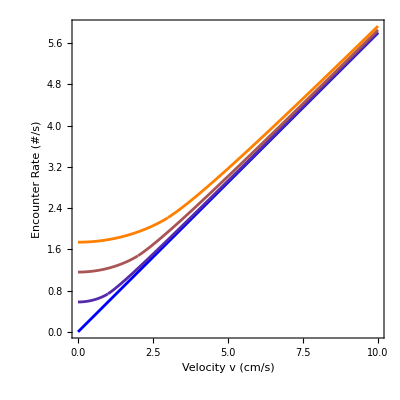

```mathematica
Plot[Evaluate@Table[Style[M2D[0.01,v,u,sculD],Blend[{Blue,Orange},u/3]],{u,0,3,1}],{v,0,10}, 
PlotRange->{All, {-0.2,All}},AspectRatio->1, Frame->True,FrameLabel->{"Velocity v (cm/s)","Encounter Rate (#/s)"}, LabelStyle->{Black,20}]
```

#### M3D

Power::infy: Infinite expression 1/0 encountered.

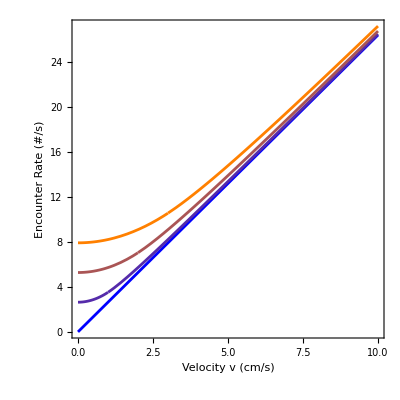

```mathematica
Plot[Evaluate@Table[Style[M3D[0.001,v,u,sculD],Blend[{Blue,Orange},u/3]],{u,0,3,1}],{v,0,10}, 
PlotRange->{All, {-0.2,All}}, AspectRatio->1, Frame->True,FrameLabel->{"Velocity v (cm/s)","Encounter Rate (#/s)"}, LabelStyle->{Black,20}]
```

#### Sculpin

```mathematica
FindRoot[Aint[scultmax, sculv,s,sculD] == 0,{s,1}]
```

{s→2.42761+0. ⅈ}

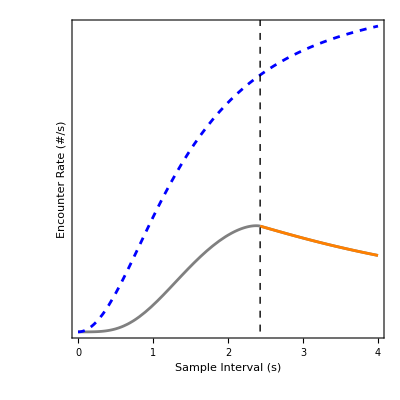

```mathematica
Show[
Plot[I2Dm[mN,0,s,scultmax, sculv, sculD],{s,0,4}, PlotStyle->Gray],
Plot[C2Dm[mN,0,s,scultmax, sculv, sculD],{s,0,4}, PlotStyle->{Blue,Dashed}],
Plot[D2Dm[mN,0,s,scultmax, sculv, sculD],{s,FindRoot[Re[Aint[scultmax, sculv,s,sculD]]==0,{s,1}][[1]][[2]],4}, PlotStyle->Orange, PlotRange->{{1.8,4},All}],
Graphics[{Dashed, Black, InfiniteLine[{{FindRoot[Re[Aint[scultmax, sculv,s,sculD]]==0,{s,1}][[1]][[2]],0},{FindRoot[Re[Aint[scultmax, sculv,s,sculD]]==0,{s,1}][[1]][[2]],50}}]}],
PlotRange->All, AspectRatio->1, Frame->True,FrameTicks->{True,False}, FrameLabel->{"Sample Interval (s)","Encounter Rate (#/s)"},LabelStyle->{20,Black}
]
```

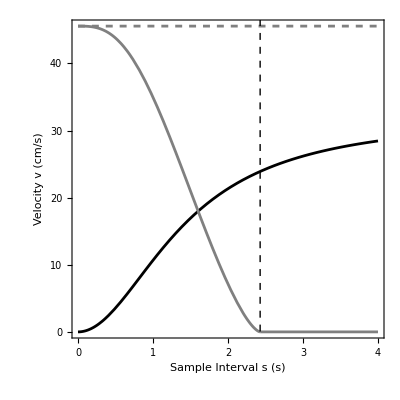

```mathematica
Show[
Plot[Pi sculD^2,{s,0,4}, PlotStyle->{Gray, Dashed}],
Plot[Velo[s,scultmax,sculv]2sculD,{s,0,4}, PlotStyle->Black],
Plot[Re[Aint[scultmax,sculv,s, sculD]],{s,0,4}, PlotStyle->Gray],
Graphics[{Dashed, Black, InfiniteLine[{{FindRoot[Re[Aint[scultmax, sculv,s,sculD]]==0,{s,1}][[1]][[2]],0},{FindRoot[Re[Aint[scultmax, sculv,s,sculD]]==0,{s,1}][[1]][[2]],50}}]}],
PlotRange->All, AspectRatio->1, Frame->True,FrameTicks->{Automatic,{{0,"0"},{580,"10"},{1160,"20"},{1740,"30"},{2320,"40"}}},FrameLabel->{"Sample Interval s (s)","Velocity v (cm/s)"},LabelStyle->{18,Black}
]
```

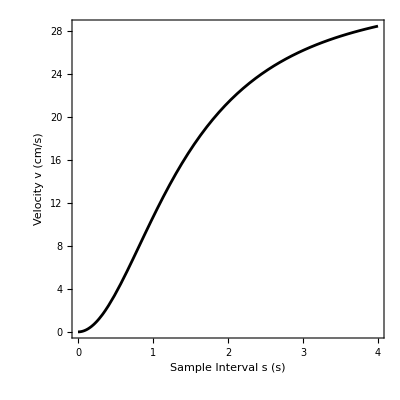

```mathematica
Show[
Plot[Velo[s,scultmax,sculv],{s,0,4}, PlotStyle->Black],
PlotRange->All, AspectRatio->1, Frame->True,FrameLabel->{"Sample Interval s (s)","Velocity v (cm/s)"},LabelStyle->{18,Black}
]
```

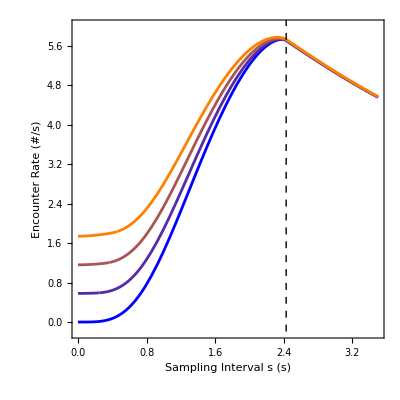

```mathematica
Show[
Plot[Evaluate@Table[Style[I2Dm[0.01,u,s,scultmax, sculv, sculD],Blend[{Blue,Orange},u/3]],{u,0,3,1}],{s,0,3.5}, 
PlotRange->{All, {-0.2,6}},AspectRatio->1, Frame->True,FrameLabel->{"Sampling Interval s (s)","Encounter Rate (#/s)"}, LabelStyle->{Black,20}],
Graphics[{Dashed, Black, InfiniteLine[{{FindRoot[Re[Aint[scultmax, sculv,s,sculD]]==0,{s,1}][[1]][[2]],0},{FindRoot[Re[Aint[scultmax, sculv,s,sculD]]==0,{s,1}][[1]][[2]],50}}]}]]
```

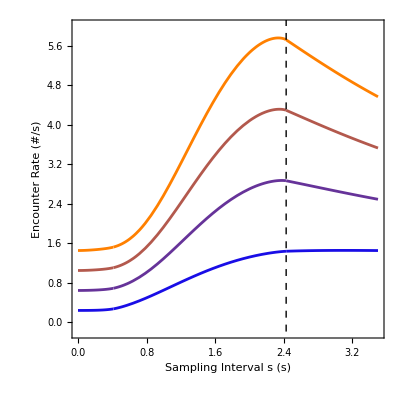

```mathematica
Show[
Plot[Evaluate@Table[Style[(I2Dm[0.01-f,bmv,s,scultmax, sculv, sculD]+C2Dm[f,bmv,s,scultmax,sculv,sculmin]),Blend[{Orange,Blue},f/0.01]],{f,0,0.01,0.003}],{s,0,3.5}, 
PlotRange->{All, {-0.2,6}},AspectRatio->1, Frame->True,FrameLabel->{"Sampling Interval s (s)","Encounter Rate (#/s)"}, LabelStyle->{Black,20}],
Graphics[{Dashed, Black, InfiniteLine[{{FindRoot[Re[Aint[scultmax, sculv,s,sculD]]==0,{s,1}][[1]][[2]],0},{FindRoot[Re[Aint[scultmax, sculv,s,sculD]]==0,{s,1}][[1]][[2]],50}}]}]]
```

```mathematica
Show[
Plot3D[sculN S2D[mN,Velo[s,scultmax,sculv],sculD],{s,0,3},{mN,0,0.01},PlotPoints->45,PlotLegends->Automatic,PlotStyle->{Opacity[0.35],Blue},
AspectRatio->1, LabelStyle->{Black,20}, Mesh->False],
Plot3D[sculN I2Dm[mN,0,s,scultmax, sculv, sculD],{s,0,3},{mN,0,0.01},PlotPoints->45,PlotLegends->Automatic,PlotStyle->{Opacity[0.35],Orange},
AspectRatio->1, LabelStyle->{Black,20}, Mesh->False],
PlotRange->All,Ticks->{Automatic,{{0.000,"0"},{0.005,"50"},{0.01,"100"}},Automatic}
]
```

-Graphics3D-

## ER & Migration

```mathematica
PLARGE[t_?NumericQ,mp_?NumericQ,mN_?NumericQ, v_?NumericQ]:= smeltN*T2[M3D[mp * mN/4,v,bmv,SmeltD[t,depx[t],dsens]],smeltESlarge,smeltH];

PSMALL[t_?NumericQ,mp_?NumericQ,mN_?NumericQ, v_?NumericQ]:= smeltN*T2[M3D[mp * mN/4,v,smv,SmeltD[t,depx[t],dsens]],smeltESsmall,smeltH];

BLARGE[migprop_?NumericQ,mN_?NumericQ,alpha_?NumericQ,s_?NumericQ,ESa_?NumericQ,ESb_?NumericQ]:=sculN*(T2[Re[I2Dm[(1-migprop)*mN*alpha,0,s,scultmax,sculv,sculD]],ESa,sculH]+T2[C2Dm[(1-migprop)*mN*(1-alpha),bmv,s,scultmax,sculv,sculmin],ESb,sculH]);

BSMALL[migprop_?NumericQ,mN_?NumericQ,alpha_?NumericQ,s_?NumericQ,ESa_?NumericQ,ESb_?NumericQ]:=sculN*(T2[Re[I2Dm[(1-migprop)*mN*alpha,0,s,scultmax,sculv,sculD]],ESa,sculH]+T2[C2Dm[(1-migprop)*mN*(1-alpha),smv,s,scultmax,sculv,sculmin],ESb,sculH]);
```

```mathematica
sculs = FindRoot[Re[Aint[scultmax, sculv,s,sculD]]==0,{s,1}][[1]][[2]]
```

2.42848

### EQUAL CAPTURE SUCCESS

#### mN = 0.01

NIntegrate::inumr: The integrand PSMALL[t,mig,0.01,15] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

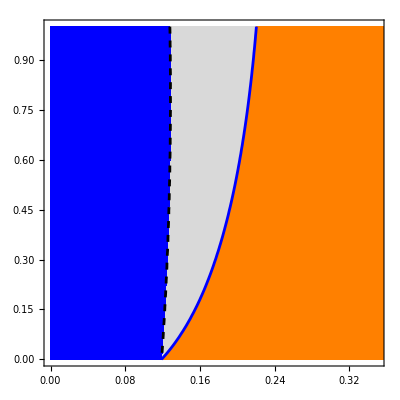

```mathematica
(* SMALL *)
mN = 0.01;
smeltESsmall = 0.72; (*smeltESsmall = 0.36*)
sculESlarge = 0.277;
conversion = 60*60; (* Converts hours to seconds, benthic X13 to serve as the integration window used for pelagic *)
Show[
(* Burrowing is five times as safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->LightGray, BoundaryStyle->None],
(* Burrowing is no more safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig -
13*conversion* BSMALL[mig,mN,alph,sculs,sculESsmall,sculESsmall]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->Orange,BoundaryStyle ->None],
(* Burrowing is five times as safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig -
13*conversion* BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)<0, {mig,0,0.5},{alph,0,1},
PlotStyle->Blue,BoundaryStyle ->None],

ContourPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},PlotPoints->20,
ContourStyle->{Black,Dashed}],
ContourPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall,sculESsmall]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},PlotPoints->20,
ContourStyle->Blue],

Frame->True,LabelStyle->{Black,16},PlotRange->{{0,0.35},All}
]
```

NIntegrate::inumr: The integrand PLARGE[t,mig,0.01,15] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

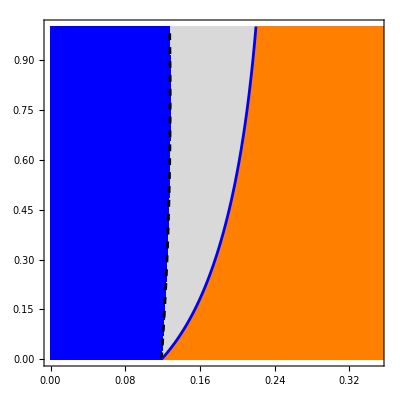

```mathematica
(* LARGE *)
smeltESlarge = 0.72; (*smeltESlarge = 0.36*)
conversion = 60*60; (* Converts hours to seconds, benthic X13 to serve as the integration window used for pelagic *)
Show[
RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->LightGray, BoundaryStyle->None],

RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge,sculESlarge]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->Orange,BoundaryStyle ->None],

RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)<0, {mig,0,0.5},{alph,0,1},
PlotStyle->Blue,BoundaryStyle ->None],

ContourPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},
ContourStyle->{Black,Dashed}],
ContourPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge,sculESlarge]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},
ContourStyle->Blue, PlotPoints->100],

Frame->True,LabelStyle->{Black,16},PlotRange->{{0,0.35},All}
]
```

#### mN = 0.05

NIntegrate::inumr: The integrand PSMALL[t,mig,0.05,15] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

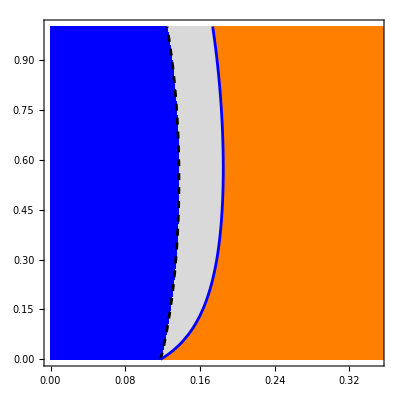

```mathematica
(* SMALL *)
mN = 0.05;
smeltESsmall = 0.72; (*smeltESsmall = 0.36*)
sculESlarge = 0.277;
conversion = 60*60; (* Converts hours to seconds, benthic X13 to serve as the integration window used for pelagic *)
Show[
(* Burrowing is five times as safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->LightGray, BoundaryStyle->None],
(* Burrowing is no more safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig -
13*conversion* BSMALL[mig,mN,alph,sculs,sculESsmall,sculESsmall]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->Orange,BoundaryStyle ->None],
(* Burrowing is five times as safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig -
13*conversion* BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)<0, {mig,0,0.5},{alph,0,1},
PlotStyle->Blue,BoundaryStyle ->None],

ContourPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},PlotPoints->20,
ContourStyle->{Black,Dashed}],
ContourPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall,sculESsmall]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},PlotPoints->20,
ContourStyle->Blue],

Frame->True,LabelStyle->{Black,16},PlotRange->{{0,0.35},All}
]
```

NIntegrate::inumr: The integrand PLARGE[t,mig,0.05,15] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

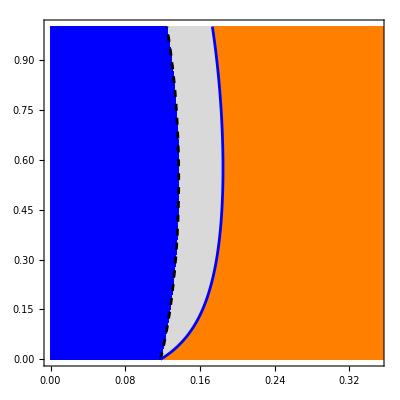

```mathematica
(* LARGE *)
smeltESlarge = 0.72; (*smeltESlarge = 0.36*)
conversion = 60*60; (* Converts hours to seconds, benthic X13 to serve as the integration window used for pelagic *)
Show[
RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->LightGray, BoundaryStyle->None],

RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge,sculESlarge]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->Orange,BoundaryStyle ->None],

RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)<0, {mig,0,0.5},{alph,0,1},
PlotStyle->Blue,BoundaryStyle ->None],

ContourPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},
ContourStyle->{Black,Dashed}],
ContourPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge,sculESlarge]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},
ContourStyle->Blue, PlotPoints->100],

Frame->True,LabelStyle->{Black,16},PlotRange->{{0,0.35},All}
]
```

#### mN = 0.09

NIntegrate::inumr: The integrand PSMALL[t,mig,0.09,15] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

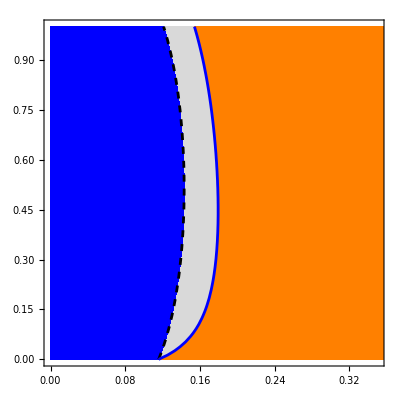

```mathematica
(* SMALL *)
mN = 0.09;
smeltESsmall = 0.72; (*smeltESsmall = 0.36*)
sculESlarge = 0.277;
conversion = 60*60; (* Converts hours to seconds, benthic X13 to serve as the integration window used for pelagic *)
Show[
(* Burrowing is five times as safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->LightGray, BoundaryStyle->None],
(* Burrowing is no more safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig -
13*conversion* BSMALL[mig,mN,alph,sculs,sculESsmall,sculESsmall]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->Orange,BoundaryStyle ->None],
(* Burrowing is five times as safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig -
13*conversion* BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)<0, {mig,0,0.5},{alph,0,1},
PlotStyle->Blue,BoundaryStyle ->None],

ContourPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},PlotPoints->20,
ContourStyle->{Black,Dashed}],
ContourPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall,sculESsmall]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},PlotPoints->20,
ContourStyle->Blue],

Frame->True,LabelStyle->{Black,16},PlotRange->{{0,0.35},All}
]
```

NIntegrate::inumr: The integrand PLARGE[t,mig,0.09,15] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

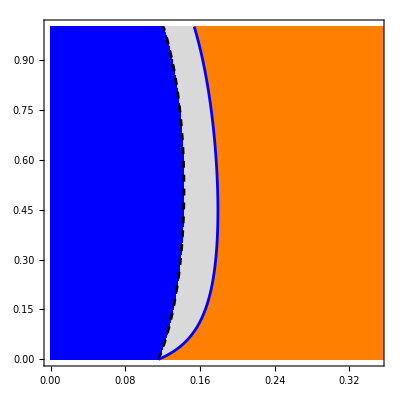

```mathematica
(* LARGE *)
smeltESlarge = 0.72; (*smeltESlarge = 0.36*)
conversion = 60*60; (* Converts hours to seconds, benthic X13 to serve as the integration window used for pelagic *)
Show[
RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->LightGray, BoundaryStyle->None],

RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge,sculESlarge]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->Orange,BoundaryStyle ->None],

RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)<0, {mig,0,0.5},{alph,0,1},
PlotStyle->Blue,BoundaryStyle ->None],

ContourPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},
ContourStyle->{Black,Dashed}],
ContourPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge,sculESlarge]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},
ContourStyle->Blue, PlotPoints->100],

Frame->True,LabelStyle->{Black,16},PlotRange->{{0,0.35},All}
]
```

### DIFFERENT CAPTURE SUCCESS

#### mN = 0.01

NIntegrate::inumr: The integrand PSMALL[t,mig,0.01,15] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

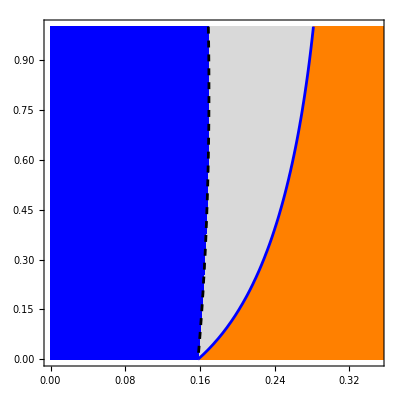

```mathematica
(* SMALL *)
mN = 0.01;
smeltESsmall = 0.36; (*smeltESsmall = 0.36*)
sculESlarge = 0.1385;
conversion = 60*60; (* Converts hours to seconds, benthic X13 to serve as the integration window used for pelagic *)
Show[
(* Burrowing is five times as safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->LightGray, BoundaryStyle->None],
(* Burrowing is no more safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig -
13*conversion* BSMALL[mig,mN,alph,sculs,sculESsmall,sculESsmall]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->Orange,BoundaryStyle ->None],
(* Burrowing is five times as safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig -
13*conversion* BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)<0, {mig,0,0.5},{alph,0,1},
PlotStyle->Blue,BoundaryStyle ->None],

ContourPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},PlotPoints->20,
ContourStyle->{Black,Dashed}],
ContourPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall,sculESsmall]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},PlotPoints->20,
ContourStyle->Blue],

Frame->True,LabelStyle->{Black,16},PlotRange->{{0,0.35},All}
]
```

NIntegrate::inumr: The integrand PLARGE[t,mig,0.01,15] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

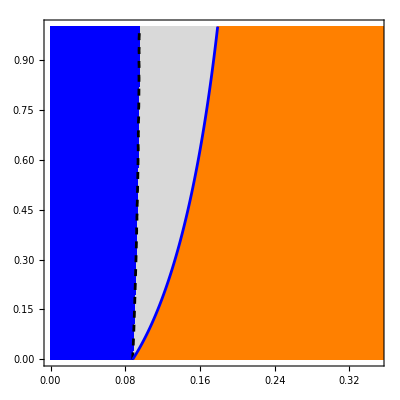

```mathematica
(* LARGE *)
smeltESlarge = 0.72; (*smeltESlarge = 0.36*)
conversion = 60*60; (* Converts hours to seconds, benthic X13 to serve as the integration window used for pelagic *)
Show[
RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->LightGray, BoundaryStyle->None],

RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge,sculESlarge]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->Orange,BoundaryStyle ->None],

RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)<0, {mig,0,0.5},{alph,0,1},
PlotStyle->Blue,BoundaryStyle ->None],

ContourPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},
ContourStyle->{Black,Dashed}],
ContourPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge,sculESlarge]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},
ContourStyle->Blue, PlotPoints->100],

Frame->True,LabelStyle->{Black,16},PlotRange->{{0,0.35},All}
]
```

#### mN = 0.05

NIntegrate::inumr: The integrand PSMALL[t,mig,0.05,15] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

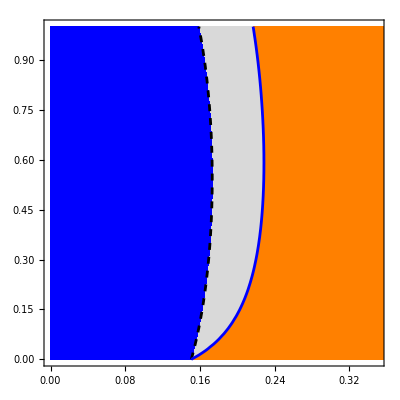

```mathematica
(* SMALL *)
mN = 0.05;
smeltESsmall = 0.36; (*smeltESsmall = 0.36*)
sculESlarge = 0.1385;
conversion = 60*60; (* Converts hours to seconds, benthic X13 to serve as the integration window used for pelagic *)
Show[
(* Burrowing is five times as safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->LightGray, BoundaryStyle->None],
(* Burrowing is no more safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig -
13*conversion* BSMALL[mig,mN,alph,sculs,sculESsmall,sculESsmall]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->Orange,BoundaryStyle ->None],
(* Burrowing is five times as safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig -
13*conversion* BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)<0, {mig,0,0.5},{alph,0,1},
PlotStyle->Blue,BoundaryStyle ->None],

ContourPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},PlotPoints->20,
ContourStyle->{Black,Dashed}],
ContourPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall,sculESsmall]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},PlotPoints->20,
ContourStyle->Blue],

Frame->True,LabelStyle->{Black,16},PlotRange->{{0,0.35},All}
]
```

NIntegrate::inumr: The integrand PLARGE[t,mig,0.05,15] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

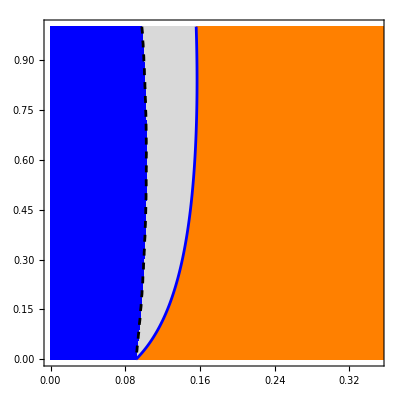

```mathematica
(* LARGE *)
smeltESlarge = 0.72; (*smeltESlarge = 0.36*)
conversion = 60*60; (* Converts hours to seconds, benthic X13 to serve as the integration window used for pelagic *)
Show[
RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->LightGray, BoundaryStyle->None],

RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge,sculESlarge]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->Orange,BoundaryStyle ->None],

RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)<0, {mig,0,0.5},{alph,0,1},
PlotStyle->Blue,BoundaryStyle ->None],

ContourPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},
ContourStyle->{Black,Dashed}],
ContourPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge,sculESlarge]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},
ContourStyle->Blue, PlotPoints->100],

Frame->True,LabelStyle->{Black,16},PlotRange->{{0,0.35},All}
]
```

#### mN = 0.09

NIntegrate::inumr: The integrand PSMALL[t,mig,0.09,15] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

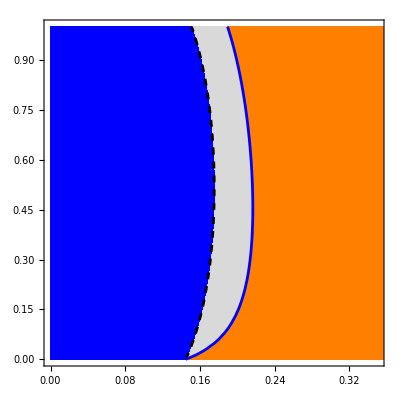

```mathematica
(* SMALL *)
mN = 0.09;
smeltESsmall = 0.36; (*smeltESsmall = 0.36*)
sculESlarge = 0.1385;
conversion = 60*60; (* Converts hours to seconds, benthic X13 to serve as the integration window used for pelagic *)
Show[
(* Burrowing is five times as safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->LightGray, BoundaryStyle->None],
(* Burrowing is no more safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig -
13*conversion* BSMALL[mig,mN,alph,sculs,sculESsmall,sculESsmall]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->Orange,BoundaryStyle ->None],
(* Burrowing is five times as safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig -
13*conversion* BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)<0, {mig,0,0.5},{alph,0,1},
PlotStyle->Blue,BoundaryStyle ->None],

ContourPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},PlotPoints->20,
ContourStyle->{Black,Dashed}],
ContourPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall,sculESsmall]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},PlotPoints->20,
ContourStyle->Blue],

Frame->True,LabelStyle->{Black,16},PlotRange->{{0,0.35},All}
]
```

NIntegrate::inumr: The integrand PLARGE[t,mig,0.09,15] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

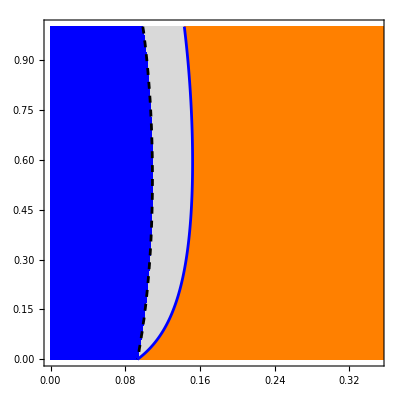

```mathematica
(* LARGE *)
smeltESlarge = 0.72; (*smeltESlarge = 0.36*)
conversion = 60*60; (* Converts hours to seconds, benthic X13 to serve as the integration window used for pelagic *)
Show[
RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->LightGray, BoundaryStyle->None],

RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge,sculESlarge]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->Orange,BoundaryStyle ->None],

RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)<0, {mig,0,0.5},{alph,0,1},
PlotStyle->Blue,BoundaryStyle ->None],

ContourPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},
ContourStyle->{Black,Dashed}],
ContourPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge,sculESlarge]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},
ContourStyle->Blue, PlotPoints->100],

Frame->True,LabelStyle->{Black,16},PlotRange->{{0,0.35},All}
]
```

### PRED ESTIMATES: VARIED (A3)

```mathematica
mN = 0.05;
smeltESsmall = 0.36; (*smeltESsmall = 0.36*)
sculESlarge = 0.1385;
conversion = 60*60; (* Converts hours to seconds, benthic X13 to serve as the integration window used for pelagic *)
```

#### More Smelt

```mathematica
sculN =0.00000001; (*0.00000001*)
smeltN =0.0000003; (*0.00000015*)
```

NIntegrate::inumr: The integrand PSMALL[t,mig,0.05,15] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

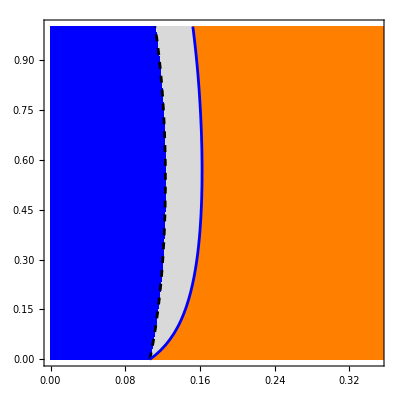

```mathematica
(* SMALL *)
Show[
(* Burrowing is five times as safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->LightGray, BoundaryStyle->None],
(* Burrowing is no more safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig -
13*conversion* BSMALL[mig,mN,alph,sculs,sculESsmall,sculESsmall]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->Orange,BoundaryStyle ->None],
(* Burrowing is five times as safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig -
13*conversion* BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)<0, {mig,0,0.5},{alph,0,1},
PlotStyle->Blue,BoundaryStyle ->None],

ContourPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},PlotPoints->20,
ContourStyle->{Black,Dashed}],
ContourPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall,sculESsmall]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},PlotPoints->20,
ContourStyle->Blue],

Frame->True,LabelStyle->{Black,16},PlotRange->{{0,0.35},All}
]
```

NIntegrate::inumr: The integrand PLARGE[t,mig,0.05,15] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

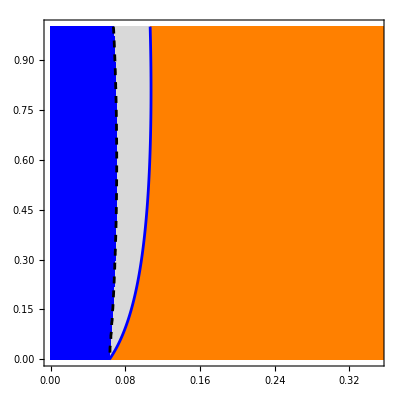

```mathematica
(* LARGE *)
smeltESlarge = 0.72; (*smeltESlarge = 0.36*)
conversion = 60*60; (* Converts hours to seconds, benthic X13 to serve as the integration window used for pelagic *)
Show[
RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->LightGray, BoundaryStyle->None],

RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge,sculESlarge]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->Orange,BoundaryStyle ->None],

RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)<0, {mig,0,0.5},{alph,0,1},
PlotStyle->Blue,BoundaryStyle ->None],

ContourPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},
ContourStyle->{Black,Dashed}],
ContourPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge,sculESlarge]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},
ContourStyle->Blue, PlotPoints->100],

Frame->True,LabelStyle->{Black,16},PlotRange->{{0,0.35},All}
]
```

#### More Sculpin

```mathematica
sculN =0.00000002; (*0.00000001*)
smeltN =0.00000015; (*0.00000015*)
```

NIntegrate::inumr: The integrand PSMALL[t,mig,0.05,15] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

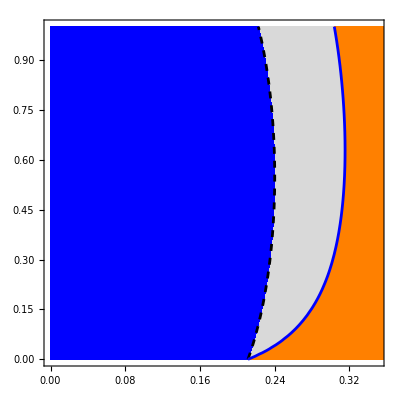

```mathematica
(* SMALL *)
Show[
(* Burrowing is five times as safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->LightGray, BoundaryStyle->None],
(* Burrowing is no more safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig -
13*conversion* BSMALL[mig,mN,alph,sculs,sculESsmall,sculESsmall]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->Orange,BoundaryStyle ->None],
(* Burrowing is five times as safe *)
RegionPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig -
13*conversion* BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)<0, {mig,0,0.5},{alph,0,1},
PlotStyle->Blue,BoundaryStyle ->None],

ContourPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall/5,sculESsmall]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},PlotPoints->20,
ContourStyle->{Black,Dashed}],
ContourPlot[conversion*NIntegrate[PSMALL[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BSMALL[mig,mN,alph,sculs,sculESsmall,sculESsmall]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},PlotPoints->20,
ContourStyle->Blue],

Frame->True,LabelStyle->{Black,16},PlotRange->{{0,0.35},All}
]
```

NIntegrate::inumr: The integrand PLARGE[t,mig,0.05,15] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

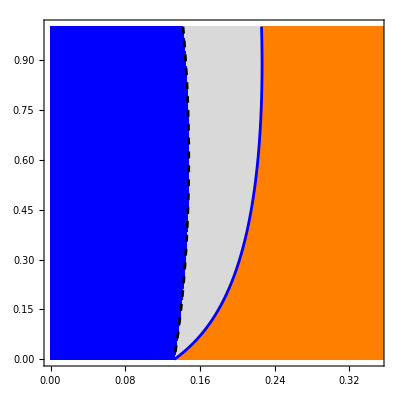

```mathematica
(* LARGE *)
smeltESlarge = 0.72; (*smeltESlarge = 0.36*)
conversion = 60*60; (* Converts hours to seconds, benthic X13 to serve as the integration window used for pelagic *)
Show[
RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->LightGray, BoundaryStyle->None],

RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge,sculESlarge]/mN*(1-mig)>0, {mig,0,0.5},{alph,0,1},
PlotStyle->Orange,BoundaryStyle ->None],

RegionPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)<0, {mig,0,0.5},{alph,0,1},
PlotStyle->Blue,BoundaryStyle ->None],

ContourPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge/5,sculESlarge]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},
ContourStyle->{Black,Dashed}],
ContourPlot[conversion*NIntegrate[PLARGE[t,mig,mN,smeltv],{t,18.5,31.5}]/mN*mig - 
13*conversion*BLARGE[mig,mN,alph,sculs,sculESlarge,sculESlarge]/mN*(1-mig)==0, {mig,0,0.5},{alph,0,1},
ContourStyle->Blue, PlotPoints->100],

Frame->True,LabelStyle->{Black,16},PlotRange->{{0,0.35},All}
]
```

### Migration Proportion (Appendix S2)

```mathematica
mN = 0.01;
palt1 = Plot[
FindRoot[NIntegrate[pelint[t,migprop,smeltN,mN, Velo[s,scultmax,sculv]],{t,18.5,31.5}]/mN*migprop == 13*benalt[19.5,migprop,sculN,mN,s]/mN*(1-migprop),{migprop,0.5}][[1]][[2]],
{s,0,5},PlotStyle->{Orange}];
palt2 = Plot[
FindRoot[NIntegrate[pelint[t,migprop,smeltN,mN, Velo[s,scultmax,sculv]],{t,18.5,31.5}] == 13*benalt[19.5,migprop,sculN,mN,s],{migprop,0.5}][[1]][[2]],
{s,0,5},PlotStyle->Orange];
p1 = Plot[
FindRoot[NIntegrate[pelint[t,migprop,smeltN,mN, Velo[s,scultmax,sculv]],{t,18.5,31.5}]/mN*migprop == 13*benint[19.5,migprop,sculN,mN,s]/mN*(1-migprop),{migprop,0.5}][[1]][[2]],
{s,0,5},PlotStyle->{Blue}];
p2 = Plot[
FindRoot[NIntegrate[pelint[t,migprop,smeltN,mN, Velo[s,scultmax,sculv]],{t,18.5,31.5}] == 13*benint[19.5,migprop,sculN,mN,s],{migprop,0.5}][[1]][[2]],
{s,0,5},PlotStyle->Blue];
palt15 = Plot[
FindRoot[NIntegrate[pelint[t,migprop,smeltN,mN, Velo[s,scultmax,sculv]],{t,18.5,31.5}]/mN*migprop == 13*benalt[19.5,migprop,sculN,mN,s]/mN*(1-migprop),{migprop,0.5}][[1]][[2]],
{s,0,0.8},PlotStyle->{Orange}];
palt25 = Plot[
FindRoot[NIntegrate[pelint[t,migprop,smeltN,mN, Velo[s,scultmax,sculv]],{t,18.5,31.5}] == 13*benalt[19.5,migprop,sculN,mN,s],{migprop,0.5}][[1]][[2]],
{s,0,0.8},PlotStyle->Orange];
```

NIntegrate::inumr: The integrand pelint[t,migprop,1.5×10^-7,0.01,1.66931×10^-7] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

NIntegrate::inumr: The integrand pelint[t,0.5,1.5×10^-7,0.01,1.66931×10^-7] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindRoot::nlnum: The function value {-(1.625×10^-7 sculES)/(1.+1.4×10^-8 sculES)+50. NIntegrate[pelint[t,migprop,1.5×10^-7,0.01,Velo[s,2.,32.]],{t,18.5,31.5}]} is not a list of numbers with dimensions {1} at {migprop} = {0.5}.

FindRoot::nlnum: The function value {-(3.19195×10^-7 sculES)/(1.+2.74999×10^-8 sculES)+50. NIntegrate[pelint[t,migprop,1.5×10^-7,0.01,Velo[s,2.,32.]],{t,18.5,31.5}]} is not a list of numbers with dimensions {1} at {migprop} = {0.5}.

FindRoot::nlnum: The function value {-(7.8115×10^-7 sculES)/(1.+6.72991×10^-8 sculES)+50. NIntegrate[pelint[t,migprop,1.5×10^-7,0.01,Velo[s,2.,32.]],{t,18.5,31.5}]} is not a list of numbers with dimensions {1} at {migprop} = {0.5}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

NIntegrate::inumr: The integrand pelint[t,migprop,1.5×10^-7,0.01,1.66931×10^-7] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

NIntegrate::inumr: The integrand pelint[t,0.5,1.5×10^-7,0.01,1.66931×10^-7] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindRoot::nlnum: The function value {-(3.25×10^-9 sculES)/(1.+1.4×10^-8 sculES)+NIntegrate[pelint[t,migprop,1.5×10^-7,0.01,Velo[s,2.,32.]],{t,18.5,31.5}]} is not a list of numbers with dimensions {1} at {migprop} = {0.5}.

FindRoot::nlnum: The function value {-(6.3839×10^-9 sculES)/(1.+2.74999×10^-8 sculES)+NIntegrate[pelint[t,migprop,1.5×10^-7,0.01,Velo[s,2.,32.]],{t,18.5,31.5}]} is not a list of numbers with dimensions {1} at {migprop} = {0.5}.

FindRoot::nlnum: The function value {-(1.5623×10^-8 sculES)/(1.+6.72991×10^-8 sculES)+NIntegrate[pelint[t,migprop,1.5×10^-7,0.01,Velo[s,2.,32.]],{t,18.5,31.5}]} is not a list of numbers with dimensions {1} at {migprop} = {0.5}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

NIntegrate::inumr: The integrand pelint[t,migprop,1.5×10^-7,0.01,1.66931×10^-7] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

NIntegrate::inumr: The integrand pelint[t,0.5,1.5×10^-7,0.01,1.66931×10^-7] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindRoot::nlnum: The function value {-(1.625×10^-7 sculES)/(1.+1.4×10^-8 sculES)+50. NIntegrate[pelint[t,migprop,1.5×10^-7,0.01,Velo[s,2.,32.]],{t,18.5,31.5}]} is not a list of numbers with dimensions {1} at {migprop} = {0.5}.

FindRoot::nlnum: The function value {-(1.6325×10^-7 sculES)/(1.+1.40646×10^-8 sculES)+50. NIntegrate[pelint[t,migprop,1.5×10^-7,0.01,Velo[s,2.,32.]],{t,18.5,31.5}]} is not a list of numbers with dimensions {1} at {migprop} = {0.5}.

FindRoot::nlnum: The function value {-(1.74122×10^-7 sculES)/(1.+1.50012×10^-8 sculES)+50. NIntegrate[pelint[t,migprop,1.5×10^-7,0.01,Velo[s,2.,32.]],{t,18.5,31.5}]} is not a list of numbers with dimensions {1} at {migprop} = {0.5}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

NIntegrate::inumr: The integrand pelint[t,migprop,1.5×10^-7,0.01,1.66931×10^-7] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

NIntegrate::inumr: The integrand pelint[t,0.5,1.5×10^-7,0.01,1.66931×10^-7] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindRoot::nlnum: The function value {-(3.25×10^-9 sculES)/(1.+1.4×10^-8 sculES)+NIntegrate[pelint[t,migprop,1.5×10^-7,0.01,Velo[s,2.,32.]],{t,18.5,31.5}]} is not a list of numbers with dimensions {1} at {migprop} = {0.5}.

FindRoot::nlnum: The function value {-(3.265×10^-9 sculES)/(1.+1.40646×10^-8 sculES)+NIntegrate[pelint[t,migprop,1.5×10^-7,0.01,Velo[s,2.,32.]],{t,18.5,31.5}]} is not a list of numbers with dimensions {1} at {migprop} = {0.5}.

FindRoot::nlnum: The function value {-(3.48243×10^-9 sculES)/(1.+1.50012×10^-8 sculES)+NIntegrate[pelint[t,migprop,1.5×10^-7,0.01,Velo[s,2.,32.]],{t,18.5,31.5}]} is not a list of numbers with dimensions {1} at {migprop} = {0.5}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

NIntegrate::inumr: The integrand pelint[t,migprop,1.5×10^-7,0.01,4.27342×10^-9] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

NIntegrate::inumr: The integrand pelint[t,0.5,1.5×10^-7,0.01,4.27342×10^-9] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindRoot::nlnum: The function value {-(1.625×10^-7 sculES)/(1.+1.4×10^-8 sculES)+50. NIntegrate[pelint[t,migprop,1.5×10^-7,0.01,Velo[s,2.,32.]],{t,18.5,31.5}]} is not a list of numbers with dimensions {1} at {migprop} = {0.5}.

FindRoot::nlnum: The function value {-(1.66527×10^-7 sculES)/(1.+1.4347×10^-8 sculES)+50. NIntegrate[pelint[t,migprop,1.5×10^-7,0.01,Velo[s,2.,32.]],{t,18.5,31.5}]} is not a list of numbers with dimensions {1} at {migprop} = {0.5}.

FindRoot::nlnum: The function value {-(1.78588×10^-7 sculES)/(1.+1.5386×10^-8 sculES)+50. NIntegrate[pelint[t,migprop,1.5×10^-7,0.01,Velo[s,2.,32.]],{t,18.5,31.5}]} is not a list of numbers with dimensions {1} at {migprop} = {0.5}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

NIntegrate::inumr: The integrand pelint[t,migprop,1.5×10^-7,0.01,4.27342×10^-9] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

NIntegrate::inumr: The integrand pelint[t,0.5,1.5×10^-7,0.01,4.27342×10^-9] has evaluated to non-numerical values for all sampling points in the region with boundaries {{18.5,31.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindRoot::nlnum: The function value {-(3.25×10^-9 sculES)/(1.+1.4×10^-8 sculES)+NIntegrate[pelint[t,migprop,1.5×10^-7,0.01,Velo[s,2.,32.]],{t,18.5,31.5}]} is not a list of numbers with dimensions {1} at {migprop} = {0.5}.

FindRoot::nlnum: The function value {-(3.33055×10^-9 sculES)/(1.+1.4347×10^-8 sculES)+NIntegrate[pelint[t,migprop,1.5×10^-7,0.01,Velo[s,2.,32.]],{t,18.5,31.5}]} is not a list of numbers with dimensions {1} at {migprop} = {0.5}.

FindRoot::nlnum: The function value {-(3.57176×10^-9 sculES)/(1.+1.5386×10^-8 sculES)+NIntegrate[pelint[t,migprop,1.5×10^-7,0.01,Velo[s,2.,32.]],{t,18.5,31.5}]} is not a list of numbers with dimensions {1} at {migprop} = {0.5}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

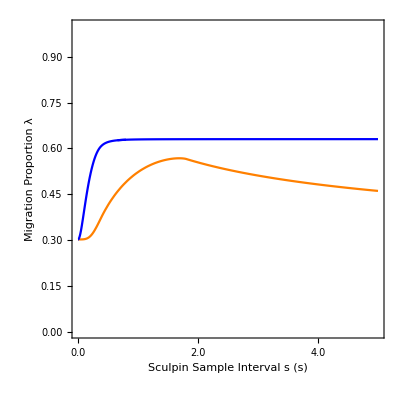

```mathematica
Show[
restylePlot[p1,PlotStyle->Orange],
restylePlot[palt1,PlotStyle->Blue],
restylePlot[palt15,PlotStyle->Blue],
AxesOrigin->{0,0},AspectRatio->1,PlotRange->{All,{0,1}}, Frame->True,FrameLabel->{"Sculpin Sample Interval s (s)","Migration Proportion λ"}, LabelStyle->{20,Black},
FrameTicks->{{{0.00,"0.0"},{1.0,"1.0"},{2.0,"2.0"},{3.0,"3.0"},{4.0,"4.0"},{5.0,"5.0"} },Automatic}
]
```

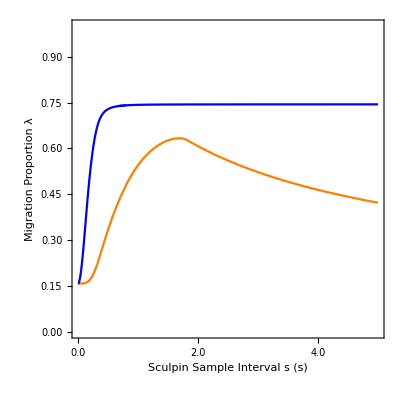

```mathematica
Show[
restylePlot[p2,PlotStyle->Orange],
restylePlot[palt2,PlotStyle->Blue],
restylePlot[palt25,PlotStyle->Blue],
AxesOrigin->{0,0},AspectRatio->1,PlotRange->{All,{0,1}}, Frame->True,FrameLabel->{"Sculpin Sample Interval s (s)","Migration Proportion λ"}, LabelStyle->{20,Black},
FrameTicks->{{{0.00,"0.0"},{1.0,"1.0"},{2.0,"2.0"},{3.0,"3.0"},{4.0,"4.0"},{5.0,"5.0"} },Automatic}
]
```